```mathematica
Arms[x1_,x2_,x3_,x4_]:=FindRoot[
{Sum[Cos[Subscript[θ, i]],{i,1,4}]==1,
Sum[Sin[Subscript[θ, i]],{i,1,4}]==0,
Sum[Cos[Subscript[θ, i]+Subscript[δ, i]],{i,1,4}]==1,
Sum[Sin[Subscript[θ, i]+Subscript[δ, i]],{i,1,4}]==0},
{{Subscript[θ, 1],x1},{Subscript[θ, 2],x2},{Subscript[θ, 3],x3},{Subscript[θ, 4],x4}},
MaxIterations->1000]
TraceOut[t_]:=FindRoot[
{2 Sum[Cos[Subscript[θ, i]],{i,1,2}]==2.5+Cos[t],
2 Sum[Sin[Subscript[θ, i]],{i,1,2}]==3 + Sin[t]},
{{Subscript[θ, 1],1},{Subscript[θ, 2],0.5}}
]
```

```mathematica
Subscript[δ, 1]=-0.07420;Subscript[δ, 2]=0.07420;Subscript[δ, 3]=-0.04497;Subscript[δ, 4]=-0.00179;
sol=Arms[3,π/5,9π/5,7π/5] (*Set 1*)
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{θ_1→51.1058,θ_2→-18.8204,θ_3→67.8663,θ_4→-34.7297}

```mathematica
Subscript[δ, 1]=-0.07420;Subscript[δ, 2]=0.02742;Subscript[δ, 3]=0.02853;Subscript[δ, 4]=-0.07487;
sol=Arms[2,1,6,4] (*Set 2 Works!*)
```

{θ_1→1.45762,θ_2→1.18995,θ_3→5.07517,θ_4→4.87357}

```mathematica
Subscript[δ, 1]=-0.02412;Subscript[δ, 2]=-0.16026;Subscript[δ, 3]=0.27843;Subscript[δ, 4]=-0.27794;
sol=Arms[RandomReal[{0,2π}],RandomReal[{0,2π}],RandomReal[{0,2π}],RandomReal[{0,2π}]] (*Set 3*)
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

{θ_1→-53.6516,θ_2→-7.46537,θ_3→-0.175675,θ_4→-11.9027}

```mathematica
Subscript[δ, 1]=0.07272;Subscript[δ, 2]=1.20678;Subscript[δ, 3]=4.78410;Subscript[δ, 4]=1.3022;
sol=Arms[2,6,0,4] (*Set 4 Works!*)
```

{θ_1→2.02505,θ_2→6.05289,θ_3→0.186444,θ_4→4.16849}

```mathematica
Subscript[δ, 1]=-0.71895;Subscript[δ, 2]=0.71895;Subscript[δ, 3]=-0.52670;Subscript[δ, 4]=-0.15747;
sol=Arms[RandomReal[{0,2π}],RandomReal[{0,2π}],RandomReal[{0,2π}],RandomReal[{0,2π}]] (*Set 5*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{θ_1→-0.447489,θ_2→0.0577355,θ_3→-4.95953,θ_4→3.79329}

{{0,0},{-0.43879,0.89859},{0.53481,0.670329},{1.51748,0.855695},{1.,1.11022×10^-16}}

{{0,0},{-0.502918,0.864334},{0.0570168,1.69287},{0.312314,0.726008},{1.,-2.22045×10^-16}}

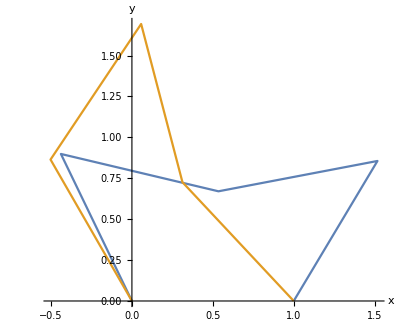

```mathematica
start = Prepend[Table[{Sum[Cos[Subscript[θ, i]]/.sol,{i,1,n}],Sum[Sin[Subscript[θ, i]]/.sol,{i,1,n}]},{n,1,4}],{0,0}]
end = Prepend[Table[{Sum[Cos[Subscript[θ, i]+Subscript[δ, i]]/.sol,{i,1,n}],Sum[Sin[Subscript[θ, i]+Subscript[δ, i]]/.sol,{i,1,n}]},{n,1,4}],{0,0}]
ListPlot[{start,end}, Joined->True,AspectRatio->Equal,AxesLabel->{"x","y"}]
```

```mathematica
m = Table[i π/7,{i,1,4}];
Table[{Sum[-Cos[m[[i]]+0.2 t^2 i],{i,1,n}],Sum[Sin[m[[i]]+0.2 t^2 i],{i,1,n}]},{n,1,4}]
```

{{-Cos[π/7+0.2 t^2],Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[(3 π)/14-0.4 t^2],Cos[(3 π)/14-0.4 t^2]+Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[π/14-0.6 t^2]-Sin[(3 π)/14-0.4 t^2],Cos[π/14-0.6 t^2]+Cos[(3 π)/14-0.4 t^2]+Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[π/14-0.6 t^2]-Sin[(3 π)/14-0.4 t^2]+Sin[π/14+0.8 t^2],Cos[π/14-0.6 t^2]+Cos[(3 π)/14-0.4 t^2]+Cos[π/14+0.8 t^2]+Sin[π/7+0.2 t^2]}}

```mathematica
anim=Animate[ListPlot[{{0,0},{-Cos[π/7+0.2 t^2],Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[(3 π)/14-0.4 t^2],Cos[(3 π)/14-0.4 t^2]+Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[π/14-0.6000000000000001 t^2]-Sin[(3 π)/14-0.4 t^2],Cos[π/14-0.6000000000000001 t^2]+Cos[(3 π)/14-0.4 t^2]+Sin[π/7+0.2 t^2]},{-Cos[π/7+0.2 t^2]-Sin[π/14-0.6000000000000001 t^2]-Sin[(3 π)/14-0.4 t^2]+Sin[π/14+0.8 t^2],Cos[π/14-0.6000000000000001 t^2]+Cos[(3 π)/14-0.4 t^2]+Cos[π/14+0.8 t^2]+Sin[π/7+0.2 t^2]}},Joined->True,PlotRange->{{-2,2},{0,4}},AspectRatio->1],{t,2,0},AnimationDirection->ForwardBackward,ControlType->None]
```

```mathematica
Export["Anim2.gif",anim]
```

Anim2.gif

{θ_1→1.66306,θ_2→0.151276}

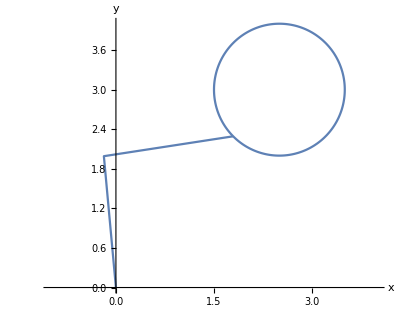

```mathematica
sol=TraceOut[5π/4]
start = Prepend[Table[{2Sum[Cos[Subscript[θ, i]]/.sol,{i,1,n}],2Sum[Sin[Subscript[θ, i]]/.sol,{i,1,n}]},{n,1,2}],{0,0}];
Show[ListPlot[{start}, Joined->True,AspectRatio->Equal,AxesLabel->{"x","y"},PlotRange->{{-1,4},{0,4}}],ParametricPlot[{2.5+Cos[t],3+Sin[t]},{t,0,2π}]]
```